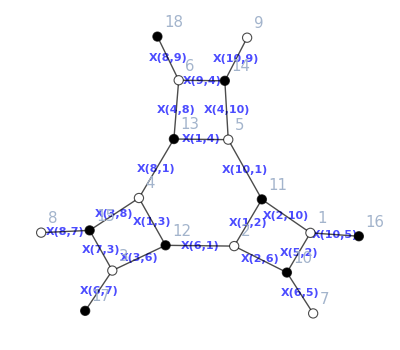

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=10;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
alternativeConnectivityMat[a_,b_,c_,d_,referencematching_:Null]:=Module[{theperf,adjacencymat,kasteleyn,perfpositions,jj,graph,cyclenodes,turnIntoContributionNothingAdded,cycles,loopnodes,extraloopnodes,toadd,loopcontributions,turnIntoContribution,connectivitymat},
If[referencematching===Null,
theperf=perfectMatchings[a,b,c,d][[lowNumberLoopsPM[a,b,c,d]]];
,theperf=referencematching;
];
adjacencymat=UpperTriangularize[getAdjacencyMatrix[a,b,c,d]];
kasteleyn=joinupKasteleyn[a,b,c,d];
perfpositions=Map[#[[{2,1}]]+{Length[kasteleyn],0}&,Position[kasteleyn,Alternatives@@Variables[theperf]]];
For[jj=1,jj≤Length[perfpositions],jj++,
adjacencymat[[Sequence@@perfpositions[[jj]]]]=1;
adjacencymat[[Sequence@@Reverse[perfpositions[[jj]]]]]=adjacencymat[[Sequence@@Reverse[perfpositions[[jj]]]]]-1;
];

graph=AdjacencyGraph[adjacencymat];

turnIntoContributionNothingAdded=Function[{pathnodes},
Module[{bigmatrix,edges,edgedirections,giveContribution,totalcontrib},
bigmatrix=Join[Join[Table[0,{iii,Length[kasteleyn]},{jjj,Length[kasteleyn]}],Transpose[kasteleyn]],Join[kasteleyn,Table[0,{iii,Dimensions[kasteleyn][[2]]},{jjj,Dimensions[kasteleyn][[2]]}]],2];
edges=Map[bigmatrix[[Sequence@@#]]&,Table[pathnodes[[{iii,iii+1}]],{iii,Length[pathnodes]-1}]];
edgedirections=Map[Ordering[#][[1]]&,Table[pathnodes[[{iii,iii+1}]],{iii,Length[pathnodes]-1}]]/.{2->-1};
giveContribution=Function[{edges,sign},
Block[{contribution},
If[sign==1,
contribution=Total[Intersection[Variables[edges],Complement[Variables[kasteleyn],Variables[theperf]]]];
,contribution=Total[Map[1/#&,Intersection[Variables[edges],Variables[theperf]]]];
];
contribution]
];
totalcontrib=Times@@MapThread[giveContribution[#1,#2]&,{edges,edgedirections}];
totalcontrib
]
];

cycles=FindCycle[graph,Infinity,All]/.{DirectedEdge->List};
loopnodes=Map[#[[Append[Range[1,Length[#],2],Length[#]]]]&,Map[Join@@#&,cycles]];
extraloopnodes={};
For[jj=2,jj≤Length[loopnodes],jj++,
toadd=Cases[Subsets[loopnodes,{jj}],zz_/;Join@@Map[Intersection@@#&,Subsets[zz,{2}]]==={}];
If[toadd==={},
Break[];
];
extraloopnodes=Join[extraloopnodes,toadd];
];
loopnodes=Join[Transpose[{loopnodes}],extraloopnodes];
loopcontributions=Map[Power[-1,Length[#]-1](Times@@#)&,Map[turnIntoContributionNothingAdded,loopnodes,{2}]];
cyclenodes=Map[Union@@#&,loopnodes];

turnIntoContribution=Function[{pathnodes},
Module[{totalcontrib},
totalcontrib=turnIntoContributionNothingAdded[pathnodes];
totalcontrib=totalcontrib/(1-Total[loopcontributions]);
totalcontrib=totalcontrib(1-Total[loopcontributions[[Flatten[Position[Map[Length[Intersection[#,pathnodes]]>0&,cyclenodes],False]]]]]);
totalcontrib
]
];

connectivitymat=Table[FindPath[graph,iii,jjj,Infinity,All],{iii,Total[Dimensions[kasteleyn]]},{jjj,Total[Dimensions[kasteleyn]]}];
connectivitymat=MapThread[Join,{connectivitymat,(DiagonalMatrix[Range[Total[Dimensions[kasteleyn]]]]/.{0->{}})/.{zz_Integer->{{zz}}}},2];
connectivitymat=Map[Total,Map[turnIntoContribution[#]&,connectivitymat,{3}],{2}];
connectivitymat
];
```

```mathematica
alternativetimings={};
normaltimings={};
```

```mathematica
For[ii=1,ii≤76,ii++,
If[ii≠33&&ii≠39&&ii≠50&&ii≠51,
Print["ii=",ii];
(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;

perfs=perfectMatchings[a,b,c,d];
srcs=Map[findSources[b,c,#]&,perfs];
multiplic=Map[Tally[srcs][[#,2]]&,Map[Position[Tally[srcs],{#,_}][[1,1]]&,srcs]];

alternative=AbsoluteTiming[alternativeConnectivityMat[a,b,c,d,Null]];
alternativetimings=Append[alternativetimings,{Length[alternative[[2]]],multiplic[[lowNumberLoopsPM[a,b,c,d]]],alternative[[1]]}];
normal=AbsoluteTiming[connectivityMatrix[a,b,c,d,Null]];
normaltimings=Append[normaltimings,{Length[normal[[2]]],multiplic[[lowNumberLoopsPM[a,b,c,d]]],normal[[1]]}];
equals={};
For[jj=1,jj≤Length[perfs],jj++,
If[Mod[jj,10]==0,Print["    jj=",jj];
];
If[multiplic[[jj]]≤3&&jj≠lowNumberLoopsPM[a,b,c,d],
alternative=AbsoluteTiming[alternativeConnectivityMat[a,b,c,d,perfs[[jj]]]];
alternativetimings=Append[alternativetimings,{Length[alternative[[2]]],multiplic[[jj]],alternative[[1]]}];
normal=AbsoluteTiming[connectivityMatrix[a,b,c,d,perfs[[jj]]]];
normaltimings=Append[normaltimings,{Length[normal[[2]]],multiplic[[jj]],normal[[1]]}];
equals=Append[equals,Simplify[alternative[[2]]==normal[[2]]]===True];
];
];
If[And@@equals=!=True,
Print["There is a PROBLEM!!!"];
];
];
];
```

ii=1

ii=2

ii=3

jj=10

ii=4

ii=5

ii=6

jj=10

ii=7

ii=8

ii=9

jj=10

jj=20

ii=10

jj=10

jj=20

jj=30

jj=40

jj=50

ii=11

jj=10

jj=20

ii=12

jj=10

jj=20

jj=30

jj=40

ii=13

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

ii=14

jj=10

jj=20

jj=30

jj=40

ii=15

jj=10

jj=20

jj=30

jj=40

ii=16

ii=17

ii=18

ii=19

ii=20

jj=10

ii=21

ii=22

jj=10

ii=23

jj=10

ii=24

jj=10

ii=25

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=26

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

jj=120

jj=130

jj=140

jj=150

jj=160

jj=170

jj=180

jj=190

jj=200

jj=210

jj=220

jj=230

jj=240

jj=250

jj=260

jj=270

jj=280

jj=290

jj=300

jj=310

jj=320

jj=330

jj=340

ii=27

jj=10

jj=20

jj=30

ii=28

jj=10

jj=20

jj=30

jj=40

ii=29

jj=10

jj=20

jj=30

jj=40

ii=30

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

ii=31

jj=10

jj=20

jj=30

ii=32

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

ii=34

ii=35

ii=36

jj=10

ii=37

jj=10

jj=20

jj=30

ii=38

jj=10

jj=20

jj=30

jj=40

ii=40

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=41

jj=10

jj=20

jj=30

ii=42

jj=10

jj=20

jj=30

ii=43

jj=10

jj=20

jj=30

jj=40

ii=44

jj=10

jj=20

jj=30

jj=40

ii=45

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=46

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=47

jj=10

jj=20

jj=30

jj=40

jj=50

ii=48

jj=10

ii=49

jj=10

ii=52

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

ii=53

jj=10

jj=20

jj=30

jj=40

ii=54

ii=55

ii=56

ii=57

jj=10

jj=20

ii=58

jj=10

jj=20

ii=59

jj=10

jj=20

jj=30

jj=40

ii=60

jj=10

jj=20

jj=30

jj=40

ii=61

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

jj=120

jj=130

jj=140

jj=150

jj=160

jj=170

jj=180

jj=190

jj=200

ii=62

jj=10

jj=20

jj=30

jj=40

ii=63

jj=10

jj=20

jj=30

ii=64

jj=10

jj=20

jj=30

ii=65

ii=66

jj=10

ii=67

jj=10

jj=20

ii=68

jj=10

jj=20

jj=30

jj=40

ii=69

jj=10

jj=20

jj=30

jj=40

ii=70

jj=10

ii=71

ii=72

jj=10

ii=73

jj=10

ii=74

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=75

jj=10

jj=20

jj=30

jj=40

ii=76

jj=10

jj=20

jj=30

jj=40

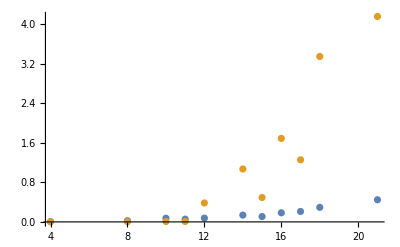

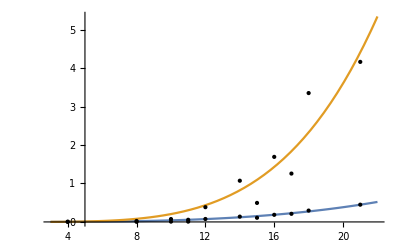

```mathematica
multiplicity=3;
datanormal=Sort[Map[Mean,GatherBy[Map[#[[{1,3}]]&,Cases[normaltimings,{_,multiplicity,_}]],First]]];
dataalternative=Sort[Map[Mean,GatherBy[Map[#[[{1,3}]]&,Cases[alternativetimings,{_,multiplicity,_}]],First]]];
ListPlot[{dataalternative,datanormal},PlotRange->All]

normalmodel=bb xx^cc;
normalfit=FindFit[datanormal,normalmodel,{bb,cc},xx];
normalline=Function[{xx},Evaluate[normalmodel/.normalfit]];

alternativemodel=bb xx^cc;
alternativefit=FindFit[dataalternative,alternativemodel,{bb,cc},xx];
alternativeline=Function[{xx},Evaluate[alternativemodel/.alternativefit]];

Plot[{alternativeline[xx],normalline[xx]},{xx,3,22},Epilog->Join[Map[Point[#,VertexColors->Blue]&,dataalternative],Map[Point[#,VertexColors->Orange]&,datanormal]],PlotRange->All]
```

{{1,0.687354},{2,1.34043},{3,4.16146}}

{{1,0.384057},{2,0.322516},{3,0.448484}}

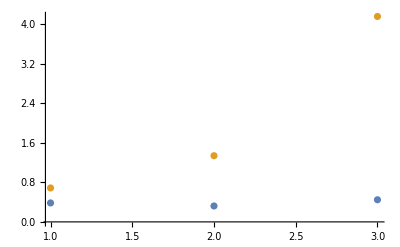

```mathematica
size=21;
datanormal=Sort[Map[Mean,GatherBy[Map[#[[{2,3}]]&,Cases[normaltimings,{size,_,_}]],First]]]
dataalternative=Sort[Map[Mean,GatherBy[Map[#[[{2,3}]]&,Cases[alternativetimings,{size,_,_}]],First]]]
ListPlot[{dataalternative,datanormal},PlotRange->All]
```

```mathematica
size=8;
Cases[normaltimings,{size,_,_}]
Cases[alternativetimings,{size,_,_}]
```

{{8,1,0.0051379},{8,1,0.0047918},{8,1,0.00275226},{8,1,0.00246546},{8,1,0.00215585},{8,1,0.00343762},{8,1,0.00292389},{8,1,0.00263366},{8,1,0.0024284},{8,1,0.00286288},{8,1,0.00276024},{8,1,0.0030881},{8,1,0.00186107},{8,1,0.00208971},{8,1,0.00326086},{8,1,0.00317363},{8,1,0.00411899},{8,1,0.00547316},{8,1,0.00471311},{8,1,0.00451697},{8,1,0.00468403},{8,1,0.00677375},{8,1,0.00305047},{8,1,0.00246489},{8,1,0.00337604},{8,1,0.0029313},{8,1,0.00379512},{8,1,0.00447364},{8,1,0.00514075},{8,1,0.00472737},{8,1,0.00668081},{8,1,0.00491211},{8,1,0.00498851},{8,1,0.00560317},{8,1,0.00360126},{8,1,0.0038778},{8,1,0.00417201},{8,1,0.00424899},{8,1,0.00433451},{8,1,0.00460535},{8,1,0.0035853},{8,1,0.00367938},{8,9,0.0161395},{8,9,0.0138491},{8,36,0.0378218},{8,36,0.0929959},{8,1,0.00893416},{8,1,0.00302481},{8,1,0.00695734},{8,1,0.0042946},{8,1,0.00496456},{8,1,0.00955281},{8,1,0.00325288}}

{{8,1,0.0266024},{8,2,0.0209028},{8,1,0.0149809},{8,1,0.0157547},{8,1,0.0124784},{8,2,0.0211685},{8,1,0.0155853},{8,1,0.017163},{8,2,0.0203537},{8,1,0.0176899},{8,2,0.0212757},{8,1,0.0163539},{8,1,0.011813},{8,1,0.0169156},{8,1,0.0194928},{8,3,0.026043},{8,3,0.023439},{8,2,0.0314175},{8,1,0.031718},{8,1,0.0305617},{8,1,0.0208561},{8,3,0.0473085},{8,2,0.0382739},{8,1,0.0199734},{8,2,0.027339},{8,2,0.0261964},{8,2,0.027107},{8,2,0.0312191},{8,1,0.0313668},{8,2,0.0393505},{8,2,0.0303165},{8,2,0.0293158},{8,2,0.0324359},{8,1,0.0246774},{8,1,0.0197077},{8,1,0.0240365},{8,2,0.02664},{8,2,0.0268008},{8,2,0.0244972},{8,1,0.0283551},{8,2,0.0422749},{8,1,0.0232542},{8,9,0.198641},{8,9,0.164649},{8,36,0.339632},{8,36,0.24169},{8,1,0.041707},{8,2,0.0441759},{8,2,0.0307025},{8,2,0.0283978},{8,2,0.0318851},{8,1,0.0239282},{8,1,0.0162091}}

```mathematica
powerExpr=Function[{inputexpr,ord},
outputexpr=Expand[Simplify[Normal[Series[inputexpr,{L1,0,ord},{L2,0,ord},{L3,0,ord},{L4,0,ord},{L5,0,ord}]]]];
outputexpr=Total[Cases[List@@outputexpr,zz_/;((zz/.{L1->ee,L2->ee,L3->ee,L4->ee,L5->ee})/.{Power[ee,pow_Integer/;pow>ord]->0})=!=0]];
outputexpr
];
powerExpr[1/(1-L1-L2-L3+L1 L2+L1 L3+L2 L3-L1 L2 L3),3]-powerExpr[1/(1-L1-L2-L3+L1 L2+L1 L3+L2 L3-L1 L2 L3),2]
```

L1^3+L1^2 L2+L1 L2^2+L2^3+L1^2 L3+L1 L2 L3+L2^2 L3+L1 L3^2+L2 L3^2+L3^3